# Tensor operators

## Coordinates

```mathematica
ClearAll[coords,sCoords];
coords={t,x,y,z};
sCoords=Drop[coords,1];
```

## 3 metric, extrinsic curvature lapse and shift

1) Metric is COvariant
2) Extrinsic curvature is COvariant
3) Shift is CONTRAvariant
4) ig is the inverse of covariant metric.

```mathematica
ClearAll[g,k,beta];
g={{gxxL,gxyL,gxzL},{gxyL,gyyL,gyzL},{gxzL,gyzL,gzzL}};
k={{kxxL,kxyL,kxzL},{kxyL,kyyL,kyzL},{kxzL,kyzL,kzzL}};
beta={betaxL,betayL,betazL};

ClearAll[ig];
ig={{igxxL,igxyL,igxzL},{igxyL,igyyL,igyzL},{igxzL,igyzL,igzzL}};
```

## Symmetry of double partial derivative

```mathematica
ClearAll[pdSyms];
pdSyms={
der[der[f_,sCoords⟦2⟧],sCoords⟦1⟧]:>der[der[f,sCoords⟦1⟧],sCoords⟦2⟧],
der[der[f_,sCoords⟦3⟧],sCoords⟦1⟧]:>der[der[f,sCoords⟦1⟧],sCoords⟦3⟧],
der[der[f_,sCoords⟦3⟧],sCoords⟦2⟧]:>der[der[f,sCoords⟦2⟧],sCoords⟦3⟧]
};
```

## Lie and covariant derivatives

Conventions:

1) Let f be scalar or tensor. Then ∂_i f=der[f,sCoords⟦i⟧]

2) Let f be scalar. Then ℒ_β f=β^i∂_i f=LieBeta[f]

3) Let f be a covariant  tensor. Then D_i f_j=∂_i f_j-Γ_ij^k f_k=sD[f,i,j]

4) Γ_ij^k=CGamma[k,i,j] is symmetric on the down indices

```mathematica
ClearAll[LieBeta];
LieBeta[f_]:=Sum[beta⟦i⟧der[f,sCoords⟦i⟧],{i,1,3}];

ClearAll[Γ]
Γ[a_,b_,c_]:=Γ[a,c,b]/;b>c;

ClearAll[sD];
sD[f_,i_,j_]:=der[f⟦j⟧,sCoords⟦i⟧]-Sum[Γ[l,i,j]f⟦l⟧,{l,1,3}];

ClearAll[CGamma]
CGamma[i_,j_,k_]:=0.5*FullSimplify[Sum[ig⟦i,l⟧(der[g⟦l,j⟧,sCoords⟦k⟧]+der[g⟦l,k⟧,sCoords⟦j⟧]-der[g⟦j,k⟧,sCoords⟦l⟧]),{l,1,3}]];
```

# Right hand sides

## Rhs for ∂_t Φ

```mathematica
ClearAll[rhsForDtPhi];
rhsForDtPhi=-2*alpL*KPhiL+LieBeta[PhiL]
```

-2 alpL KPhiL+betaxL der[PhiL,x]+betayL der[PhiL,y]+betazL der[PhiL,z]

## Rhs for ∂_t K_Φ

### Part 1

```mathematica
ClearAll[rhsForDtKPhiPart1];
rhsForDtKPhiPart1=alpL*KTraceL*KPhiL
```

alpL KPhiL KTraceL

### Part 2

```mathematica
ClearAll[collectionList];
collectionList={
der[der[PhiL,sCoords⟦1⟧],sCoords⟦1⟧],
der[der[PhiL,sCoords⟦2⟧],sCoords⟦2⟧],
der[der[PhiL,sCoords⟦3⟧],sCoords⟦3⟧],

der[der[PhiL,sCoords⟦1⟧],sCoords⟦2⟧],
der[der[PhiL,sCoords⟦1⟧],sCoords⟦3⟧],
der[der[PhiL,sCoords⟦2⟧],sCoords⟦3⟧],

der[PhiL,sCoords⟦1⟧],
der[PhiL,sCoords⟦2⟧],
der[PhiL,sCoords⟦3⟧]
};

ClearAll[rhsForDtKPhiPart2];
rhsForDtKPhiPart2=Collect[alpL*Sum[ig⟦i,j⟧sD[{der[PhiL,x],der[PhiL,y],der[PhiL,z]},i,j],{i,1,3},{j,1,3}]//.pdSyms,collectionList,FullSimplify]

ClearAll[collectionList];
```

alpL igxxL der[der[PhiL,x],x]+2 alpL igxyL der[der[PhiL,x],y]+2 alpL igxzL der[der[PhiL,x],z]+alpL igyyL der[der[PhiL,y],y]+2 alpL igyzL der[der[PhiL,y],z]+alpL igzzL der[der[PhiL,z],z]-alpL der[PhiL,x] (igxxL Γ[1,1,1]+2 igxyL Γ[1,1,2]+2 igxzL Γ[1,1,3]+igyyL Γ[1,2,2]+2 igyzL Γ[1,2,3]+igzzL Γ[1,3,3])-alpL der[PhiL,y] (igxxL Γ[2,1,1]+2 igxyL Γ[2,1,2]+2 igxzL Γ[2,1,3]+igyyL Γ[2,2,2]+2 igyzL Γ[2,2,3]+igzzL Γ[2,3,3])-alpL der[PhiL,z] (igxxL Γ[3,1,1]+2 igxyL Γ[3,1,2]+2 igxzL Γ[3,1,3]+igyyL Γ[3,2,2]+2 igyzL Γ[3,2,3]+igzzL Γ[3,3,3])

### Part 3

```mathematica
ClearAll[rhsForDtKPhiPart3];
rhsForDtKPhiPart3=Collect[Sum[ig⟦i,j⟧der[alpL,sCoords⟦i⟧]der[PhiL,sCoords⟦j⟧],{i,1,3},{j,1,3}],{igxx,igxy,igxz,igyy,igyz,igzz},FullSimplify]
```

der[alpL,x] (igxxL der[PhiL,x]+igxyL der[PhiL,y]+igxzL der[PhiL,z])+der[alpL,y] (igxyL der[PhiL,x]+igyyL der[PhiL,y]+igyzL der[PhiL,z])+der[alpL,z] (igxzL der[PhiL,x]+igyzL der[PhiL,y]+igzzL der[PhiL,z])

### Part 4

```mathematica
ClearAll[rhsForDtKPhiPart4];
rhsForDtKPhiPart4=LieBeta[KPhiL]
```

betaxL der[KPhiL,x]+betayL der[KPhiL,y]+betazL der[KPhiL,z]

# C code output

```mathematica
ClearAll[moveAndFormat];
moveAndFormat=True;
```

### Fixed part

```mathematica
ClearAll[evolutionCodeFixed];
evolutionCodeFixed=
"/*
 *  ADMScalarWave - Thorn for scalar wave evolutions in arbitrary space-times
 *  Copyright (C) 2021  Lucas Timotheo Sanches
 *
 *  This file is part of ADMScalarWave.
 *
 *  ADMScalarWave is free software: you can redistribute it and/or modify
 *  it under the terms of the GNU General Public License as published by
 *  the Free Software Foundation, either version 3 of the License, or
 *  (at your option) any later version.
 *
 *  ADMScalarWave is distributed in the hope that it will be useful,
 *  but WITHOUT ANY WARRANTY; without even the implied warranty of
 *  MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  See the
 *  GNU General Public License for more details.
 *
 *  You should have received a copy of the GNU General Public License
 *  along with Foobar.  If not, see <https://www.gnu.org/licenses/>.
 *
 * Evolve.c
 * Implements the evolution equations for the ADM-decomposed scalar wave
 * equation as presented in Eq. (19) of https://arxiv.org/abs/1806.07909.
 * Tensorial quantities and C code produced in Wolfram Mathematica.
 */

/******************* 
 * Cactus includes *
 *******************/
#include \"cctk.h\"
#include \"cctk_Arguments.h\"
#include \"cctk_Parameters.h\"

/************************* 
 * This thorn's includes *
 *************************/
#include \"Derivatives.h\"

/************** 
 * Prototypes *
 **************/
void ADMScalarWave_RHS(CCTK_ARGUMENTS);

/**********************************************
 * ADMScalarWave_RHS(CCTK_ARGUMENTS)          *
 *                                            *
 * This function computes the right hand side *
 * of the ADM scalar wave equation.           *
 *                                            *
 * Input: CCTK_ARGUMENTS (the grid functions  *
 * from interface.ccl                         *
 *                                            *
 * Output: Nothing                            *
 **********************************************/
void ADMScalarWave_RHS(CCTK_ARGUMENTS) {
  DECLARE_CCTK_ARGUMENTS;
  DECLARE_CCTK_PARAMETERS;

  /* Ghost zone indexes */
  const int gx = cctk_nghostzones[0];
  const int gy = cctk_nghostzones[1];
  const int gz = cctk_nghostzones[2];

  /* Quantities required for the derivative macros to work */
  const CCTK_REAL dx = CCTK_DELTA_SPACE(0);
  const CCTK_REAL dy = CCTK_DELTA_SPACE(1);
  const CCTK_REAL dz = CCTK_DELTA_SPACE(2);

  /* Loop indexes */
  int i = 0;
  int j = 0;
  int k = 0;
  int ijk = 0;

  /* Local ADM variables */
  CCTK_REAL alpL = 0.0;

  CCTK_REAL betaxL = 0.0;
  CCTK_REAL betayL = 0.0;
  CCTK_REAL betazL = 0.0;

  CCTK_REAL gxxL = 0.0;
  CCTK_REAL gxyL = 0.0;
  CCTK_REAL gxzL = 0.0;
  CCTK_REAL gyyL = 0.0;
  CCTK_REAL gyzL = 0.0;
  CCTK_REAL gzzL = 0.0;

  CCTK_REAL kxxL = 0.0;
  CCTK_REAL kxyL = 0.0;
  CCTK_REAL kxzL = 0.0;
  CCTK_REAL kyyL = 0.0;
  CCTK_REAL kyzL = 0.0;
  CCTK_REAL kzzL = 0.0;

  /* Local grid functions */
  CCTK_REAL PhiL = 0.0;  
  CCTK_REAL K_PhiL = 0.0;
  
  /* Local value of r */
  CCTK_REAL rL = 0.0;

  /* Local Trace of extrinsic curvature */
  CCTK_REAL KTraceL = 0.0;

  /* Local Inverse metric */
  CCTK_REAL igxxL = 0.0;
  CCTK_REAL igxyL = 0.0;
  CCTK_REAL igxzL = 0.0;
  CCTK_REAL igyyL = 0.0;
  CCTK_REAL igyzL = 0.0;
  CCTK_REAL igzzL = 0.0;
  
  /* Local metric determinant */
  CCTK_REAL gdetL = 0.0;

  /* Parts of K_Phi right hand side */
  CCTK_REAL K_Phi_rhs_p1 = 0.0;
  CCTK_REAL K_Phi_rhs_p2 = 0.0;
  CCTK_REAL K_Phi_rhs_p3 = 0.0;
  CCTK_REAL K_Phi_rhs_p4 = 0.0;

  /* Derivatives of Phi */
  CCTK_REAL d_x_Phi = 0.0;
  CCTK_REAL d_y_Phi = 0.0;
  CCTK_REAL d_z_Phi = 0.0;

  CCTK_REAL d_xx_Phi = 0.0;
  CCTK_REAL d_xy_Phi = 0.0;
  CCTK_REAL d_xz_Phi = 0.0;
    
  CCTK_REAL d_yy_Phi = 0.0;
  CCTK_REAL d_yz_Phi = 0.0;
      
  CCTK_REAL d_zz_Phi = 0.0;

  /* Derivatives of the metric */
  CCTK_REAL d_x_gxx = 0.0;
  CCTK_REAL d_y_gxx = 0.0;
  CCTK_REAL d_z_gxx = 0.0;

  CCTK_REAL d_x_gxy = 0.0;
  CCTK_REAL d_y_gxy = 0.0;
  CCTK_REAL d_z_gxy = 0.0;

  CCTK_REAL d_x_gxz = 0.0;
  CCTK_REAL d_y_gxz = 0.0;
  CCTK_REAL d_z_gxz = 0.0;

  CCTK_REAL d_x_gyy = 0.0;
  CCTK_REAL d_y_gyy = 0.0;
  CCTK_REAL d_z_gyy = 0.0;

  CCTK_REAL d_x_gyz = 0.0;
  CCTK_REAL d_y_gyz = 0.0;
  CCTK_REAL d_z_gyz = 0.0;

  CCTK_REAL d_x_gzz = 0.0;
  CCTK_REAL d_y_gzz = 0.0;
  CCTK_REAL d_z_gzz = 0.0;

  /* Derivatives of Alpha */
  CCTK_REAL d_x_alp = 0.0;
  CCTK_REAL d_y_alp = 0.0;
  CCTK_REAL d_z_alp = 0.0;

  /* Derivatives of K_Phi */
  CCTK_REAL d_x_K_Phi = 0.0;
  CCTK_REAL d_y_K_Phi = 0.0;
  CCTK_REAL d_z_K_Phi = 0.0;

  /* Christoffell symbols */
  CCTK_REAL Gamma_111 = 0;
  CCTK_REAL Gamma_112 = 0;
  CCTK_REAL Gamma_113 = 0;
  CCTK_REAL Gamma_122 = 0;
  CCTK_REAL Gamma_123 = 0;
  CCTK_REAL Gamma_133 = 0; 
  
  CCTK_REAL Gamma_211 = 0;
  CCTK_REAL Gamma_212 = 0;
  CCTK_REAL Gamma_213 = 0;
  CCTK_REAL Gamma_222 = 0;
  CCTK_REAL Gamma_223 = 0;
  CCTK_REAL Gamma_233 = 0;
  
  CCTK_REAL Gamma_311 = 0;
  CCTK_REAL Gamma_312 = 0;
  CCTK_REAL Gamma_313 = 0;
  CCTK_REAL Gamma_322 = 0;
  CCTK_REAL Gamma_323 = 0;
  CCTK_REAL Gamma_333 = 0;

  #pragma omp parallel for
  for(k = gz; k < cctk_lsh[2] - gz; k++) {
    for(j = gy; j < cctk_lsh[1] - gy; j++) {
      for(i = gx; i < cctk_lsh[0] - gx; i++) {

        ijk = CCTK_GFINDEX3D(cctkGH, i, j, k);

	    /* Assing ADM local variables */
	    alpL = alp[ijk];

	    betaxL = betax[ijk];
	    betayL = betay[ijk];
	    betazL = betaz[ijk];

    	gxxL = gxx[ijk];
	    gxyL = gxy[ijk];
	    gxzL = gxz[ijk];
	    gyyL = gyy[ijk];
	    gyzL = gyz[ijk];
	    gzzL = gzz[ijk];

    	kxxL = kxx[ijk];
	    kxyL = kxy[ijk];
	    kxzL = kxz[ijk];
	    kyyL = kyy[ijk];
	    kyzL = kyz[ijk];
	    kzzL = kzz[ijk];

        /* Assing wave eq. local variables */
        PhiL = Phi[ijk];
        K_PhiL = K_Phi[ijk];
	    rL = r[ijk];

        /* Computing the inverse metric */
	    gdetL = -(gxzL*gxzL*gyyL) + 2*gxyL*gxzL*gyzL - gxxL*gyzL*gyzL - gxyL*gxyL*gzzL + gxxL*gyyL*gzzL;
	    igxxL = (-gyzL*gyzL + gyyL*gzzL)/gdetL;
	    igxyL = (gxzL*gyzL - gxyL*gzzL)/gdetL;
	    igxzL = (-(gxzL*gyyL) + gxyL*gyzL)/gdetL;
	    igyyL = (-gxzL*gxzL + gxxL*gzzL)/gdetL;
	    igyzL = (gxyL*gxzL - gxxL*gyzL)/gdetL;
	    igzzL = (-gxyL*gxyL + gxxL*gyyL)/gdetL;

	    /* Computing the trace of extrinsic curvature */
	    KTraceL = igxxL*kxxL + 2*igxyL*kxyL + 2*igxzL*kxzL + igyyL*kyyL + 2*igyzL*kyzL + igzzL*kzzL;

        /* Derivatives of Phi */
	    d_x_Phi = D4x(Phi);
	    d_y_Phi = D4y(Phi);
	    d_z_Phi = D4z(Phi);

	    d_xx_Phi = D4xx(Phi);
	    d_xy_Phi = D4xy(Phi);
	    d_xz_Phi = D4xz(Phi);

	    d_yy_Phi = D4yy(Phi);
	    d_yz_Phi = D4yz(Phi);

	    d_zz_Phi = D4zz(Phi);

        /* Derivatives of the metric */
	    d_x_gxx = D4x(gxx);
	    d_y_gxx = D4y(gxx);
	    d_z_gxx = D4z(gxx);

	    d_x_gxy = D4x(gxy);
	    d_y_gxy = D4y(gxy);
	    d_z_gxy = D4z(gxy);

	    d_x_gxz = D4x(gxz);
	    d_y_gxz = D4y(gxz);
	    d_z_gxz = D4z(gxz);

	    d_x_gyy = D4x(gyy);
	    d_y_gyy = D4y(gyy);
	    d_z_gyy = D4z(gyy);

	    d_x_gyz = D4x(gyz);
	    d_y_gyz = D4y(gyz);
	    d_z_gyz = D4z(gyz);

	    d_x_gzz = D4x(gzz);
	    d_y_gzz = D4y(gzz);
	    d_z_gzz = D4z(gzz);

        /* Derivatives of Alpha */
	    d_x_alp = D4x(alp);
	    d_y_alp = D4y(alp);
	    d_z_alp = D4z(alp);

	    /* Derivatives of K_Phi */
	    d_x_K_Phi = D4x(K_Phi);
	    d_y_K_Phi = D4y(K_Phi);
	    d_z_K_Phi = D4z(K_Phi);

";
```

### Substitution rules

```mathematica
ClearAll[metricDerivRules]
metricDerivRules={
"der(gxxL,x)"->"d_x_gxx","der(gxxL,y)"->"d_y_gxx","der(gxxL,z)"->"d_z_gxx",
"der(gxyL,x)"->"d_x_gxy","der(gxyL,y)"->"d_y_gxy","der(gxyL,z)"->"d_z_gxy",
"der(gxzL,x)"->"d_x_gxz","der(gxzL,y)"->"d_y_gxz","der(gxzL,z)"->"d_z_gxz",
"der(gyyL,x)"->"d_x_gyy","der(gyyL,y)"->"d_y_gyy","der(gyyL,z)"->"d_z_gyy",
"der(gyzL,x)"->"d_x_gyz","der(gyzL,y)"->"d_y_gyz","der(gyzL,z)"->"d_z_gyz",
"der(gzzL,x)"->"d_x_gzz","der(gzzL,y)"->"d_y_gzz","der(gzzL,z)"->"d_z_gzz"
};
```

```mathematica
ClearAll[alphaDerivRules];
alphaDerivRules={
"der(alpL,x)"->"d_x_alp",
"der(alpL,y)"->"d_y_alp",
"der(alpL,z)"->"d_z_alp"
};
```

```mathematica
ClearAll[phiDerivRules];
phiDerivRules=
{
"der(PhiL,x)"->"d_x_Phi",
"der(PhiL,y)"->"d_y_Phi",
"der(PhiL,z)"->"d_z_Phi"
,
"der(der(PhiL,x),x)"->"d_xx_Phi",
"der(der(PhiL,x),y)"->"d_xy_Phi",
"der(der(PhiL,x),z)"->"d_xz_Phi"
,
"der(der(PhiL,y),x)"->"d_yx_Phi",
"der(der(PhiL,y),y)"->"d_yy_Phi",
"der(der(PhiL,y),z)"->"d_yz_Phi"
,
"der(der(PhiL,z),x)"->"d_zx_Phi",
"der(der(PhiL,z),y)"->"d_zy_Phi",
"der(der(PhiL,z),z)"->"d_zz_Phi"
};
```

```mathematica
ClearAll[kPhiDerivRules];
kPhiDerivRules={
"der(KPhiL,x)"->"d_x_K_Phi",
"der(KPhiL,y)"->"d_y_K_Phi",
"der(KPhiL,z)"->"d_z_K_Phi"
};
```

```mathematica
ClearAll[ΓRules];
ΓRules={
"Γ(1,1,1)"->"Gamma_111",
"Γ(1,1,2)"->"Gamma_112",
"Γ(1,1,3)"->"Gamma_113",
"Γ(1,2,2)"->"Gamma_122",
"Γ(1,2,3)"->"Gamma_123",
"Γ(1,3,3)"->"Gamma_133",

"Γ(2,1,1)"->"Gamma_211",
"Γ(2,1,2)"->"Gamma_212",
"Γ(2,1,3)"->"Gamma_213",
"Γ(2,2,2)"->"Gamma_222",
"Γ(2,2,3)"->"Gamma_223",
"Γ(2,3,3)"->"Gamma_233",

"Γ(3,1,1)"->"Gamma_311",
"Γ(3,1,2)"->"Gamma_312",
"Γ(3,1,3)"->"Gamma_313",
"Γ(3,2,2)"->"Gamma_322",
"Γ(3,2,3)"->"Gamma_323",
"Γ(3,3,3)"->"Gamma_333"
};
```

### Equations part

```mathematica
ClearAll[chirstoffellCode];
chirstoffellCode=
"/* Christoffell symbols */
  Gamma_111 = "<>StringReplace[ToString[CGamma[1,1,1],CForm],metricDerivRules]<>";\n"<>
"Gamma_112 = "<>StringReplace[ToString[CGamma[1,1,2],CForm],metricDerivRules]<>";\n"<>
"Gamma_113 = "<>StringReplace[ToString[CGamma[1,1,3],CForm],metricDerivRules]<>";\n"<>
"Gamma_122 = "<>StringReplace[ToString[CGamma[1,2,2],CForm],metricDerivRules]<>";\n"<>
"Gamma_123 = "<>StringReplace[ToString[CGamma[1,2,3],CForm],metricDerivRules]<>";\n"<>
"Gamma_133 = "<>StringReplace[ToString[CGamma[1,3,3],CForm],metricDerivRules]<>";\n\n"<>

"Gamma_211 = "<>StringReplace[ToString[CGamma[2,1,1],CForm],metricDerivRules]<>";\n"<>
"Gamma_212 = "<>StringReplace[ToString[CGamma[2,1,2],CForm],metricDerivRules]<>";\n"<>
"Gamma_213 = "<>StringReplace[ToString[CGamma[2,1,3],CForm],metricDerivRules]<>";\n"<>
"Gamma_222 = "<>StringReplace[ToString[CGamma[2,2,2],CForm],metricDerivRules]<>";\n"<>
"Gamma_223 = "<>StringReplace[ToString[CGamma[2,2,3],CForm],metricDerivRules]<>";\n"<>
"Gamma_233 = "<>StringReplace[ToString[CGamma[2,3,3],CForm],metricDerivRules]<>";\n\n"<>

"Gamma_311 = "<>StringReplace[ToString[CGamma[3,1,1],CForm],metricDerivRules]<>";\n"<>
"Gamma_312 = "<>StringReplace[ToString[CGamma[3,1,2],CForm],metricDerivRules]<>";\n"<>
"Gamma_313 = "<>StringReplace[ToString[CGamma[3,1,3],CForm],metricDerivRules]<>";\n"<>
"Gamma_322 = "<>StringReplace[ToString[CGamma[3,2,2],CForm],metricDerivRules]<>";\n"<>
"Gamma_323 = "<>StringReplace[ToString[CGamma[3,2,3],CForm],metricDerivRules]<>";\n"<>
"Gamma_333 = "<>StringReplace[ToString[CGamma[3,3,3],CForm],metricDerivRules]<>";";
```

```mathematica
ClearAll[evolutionCodeEquations1];
evolutionCodeEquations1=
"/* Part 1 of K_Phi_rhs */
   K_Phi_rhs_p1 = "<>StringReplace[ToString[rhsForDtKPhiPart1,CForm],"KPhiL"->"K_PhiL"]<>";";

ClearAll[evolutionCodeEquations2];
evolutionCodeEquations2=
"/* Part 2 of K_Phi_rhs */
   K_Phi_rhs_p2 = "<>StringReplace[ToString[rhsForDtKPhiPart2,CForm],Join[phiDerivRules,ΓRules]]<>";";

ClearAll[evolutionCodeEquations3];
evolutionCodeEquations3=
"/* Part 3 of K_Phi_rhs */
   K_Phi_rhs_p3 = "<>StringReplace[ToString[rhsForDtKPhiPart3,CForm],Join[phiDerivRules,alphaDerivRules]]<>";";

ClearAll[evolutionCodeEquations4];
evolutionCodeEquations4=
"/* Part 4 of K_Phi_rhs */
   K_Phi_rhs_p4 = "<>StringReplace[ToString[rhsForDtKPhiPart4,CForm],kPhiDerivRules]<>";";

ClearAll[evolutionCodeEquationsRhss];
evolutionCodeEquationsRhss=
"/* Phi_rhs */
   Phi_rhs[ijk] = "<>StringReplace[ToString[rhsForDtPhi,CForm],Join[phiDerivRules,{"KPhiL"->"K_PhiL"}]]<>";\n\n"<>

"/* K_Phi_rhs */
    K_Phi_rhs[ijk] = K_Phi_rhs_p1 - 0.5*K_Phi_rhs_p2 - 0.5*K_Phi_rhs_p3 + K_Phi_rhs_p4;";
```

### Full code

```mathematica
ClearAll[fullCode];
fullCode=
evolutionCodeFixed<>
chirstoffellCode<>"\n\n"<>
evolutionCodeEquations1<>"\n\n"<>
evolutionCodeEquations2<>"\n\n"<>
evolutionCodeEquations3<>"\n\n"<>
evolutionCodeEquations4<>"\n\n"<>
evolutionCodeEquationsRhss<>"\n"<>
"       }\n"<>
"    }\n"<>
"  }\n"<>
"}\n";

Export["Evolve.c",fullCode,"String"];
Run["clang-format -i -style=LLVM Evolve.c"];
```

### Move and format

```mathematica
If[moveAndFormat,
Run["mv Evolve.c ./src"];
Run["clang-format -i -style=LLVM src/*.c src/*.h"];
];
```

# Finite difference formulas

See http://www.holoborodko.com/pavel/2014/11/04/computing-mixed-derivatives-by-finite-differences

```mathematica
ClearAll[grid];
grid={{-3dx,-2dx,-1dx,0,1dx,2dx,3dx},{-3dy,-2dy,-1dy,0,1dy,2dy,3dy},{-3dz,-2dz,-1dz,0,1dz,2dz,3dz}};

ClearAll[values];
values=Flatten[Table[F[a,b,c],{a,grid⟦1⟧},{b,grid⟦2⟧},{c,grid⟦3⟧}]];

ClearAll[derivative];
derivative=FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[0,1,1],grid,values,"DifferenceOrder"->4]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧]

ClearAll[F,k];
F[a_,b_,c_]:=f[II[i+a/dx,j+b/dy,k+c/dz]];
StringReplace[ToString[derivative,CForm],{"f("->"f[","k))"->"k)]","II"->"I"}]


ClearAll[grid];
ClearAll[values];
ClearAll[derivative];
ClearAll[F];
```

1/(144 dy dz)(F[0,-2 dy,-2 dz]-8 F[0,-2 dy,-dz]+8 F[0,-2 dy,dz]-F[0,-2 dy,2 dz]-8 F[0,-dy,-2 dz]+64 F[0,-dy,-dz]-64 F[0,-dy,dz]+8 F[0,-dy,2 dz]+8 F[0,dy,-2 dz]-64 F[0,dy,-dz]+64 F[0,dy,dz]-8 F[0,dy,2 dz]-F[0,2 dy,-2 dz]+8 F[0,2 dy,-dz]-8 F[0,2 dy,dz]+F[0,2 dy,2 dz])

(f[I(i,-2 + j,-2 + k)] - 8*f[I(i,-2 + j,-1 + k)] + 8*f[I(i,-2 + j,1 + k)] - f[I(i,-2 + j,2 + k)] - 8*f[I(i,-1 + j,-2 + k)] + 64*f[I(i,-1 + j,-1 + k)] - 64*f[I(i,-1 + j,1 + k)] + 8*f[I(i,-1 + j,2 + k)] + 8*f[I(i,1 + j,-2 + k)] - 64*f[I(i,1 + j,-1 + k)] + 64*f[I(i,1 + j,1 + k)] - 8*f[I(i,1 + j,2 + k)] - f[I(i,2 + j,-2 + k)] + 8*f[I(i,2 + j,-1 + k)] - 8*f[I(i,2 + j,1 + k)] + f[I(i,2 + j,2 + k)])/(144.*dy*dz)

# Smooth transition functions (excision masks)

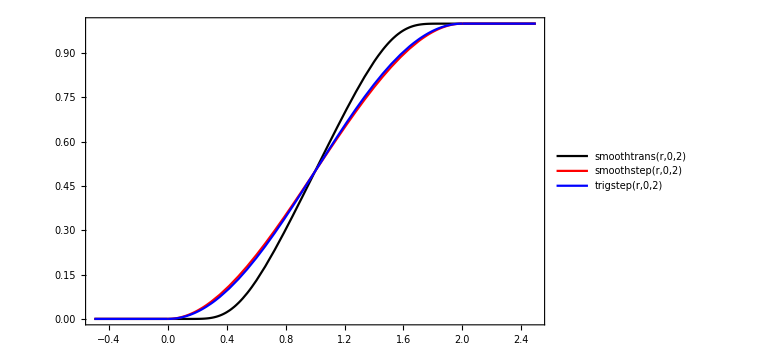

```mathematica
ClearAll[smoothtrans]
smoothtrans[r_,r0_,rh_]:=Module[
{
y,
fy,
omy,
fomy
},

y=(r-r0)/(rh-r0);
If[y>0,fy=Exp[-1.0/y],fy=0.0];

omy=1.0-y;
If[omy>0.0,fomy=Exp[-1.0/omy],fomy=0.0];

Return[fy/(fy+fomy)];
];

ClearAll[trigstep];
trigstep[r_,r0_,rh_]:=Piecewise[
{
{0,r<r0},
{1/2+1/2 Cos[(π/(rh-r0))(r-r0)+π],r0≤r≤rh},
{1,r>rh}
}
];

ClearAll[polystep];
polystep[r_,r0_,rh_]:=Piecewise[
{
{0,r<r0},
{1,r>rh},
{InterpolatingPolynomial[Table[{x,1/2+1/2 Cos[(π/(rh-r0))(x-r0)+π]},{x,r0,rh,(rh-r0)/3}],r],True}
}
];

ClearAll[smoothstep];
smoothstep[r_,r0_,rh_]:=Piecewise[
{
{1,r>rh},
{0,r<r0},
{((r-r0)/(rh-r0))*((r-r0)/(rh-r0))*(3-2*((r-r0)/(rh-r0))),True}
}
];

Plot[{smoothtrans[r,0,2],smoothstep[r,0,2],trigstep[r,0,2]},
{r,-0.5,2.5},
PlotStyle->{Directive[Black,Thick],Directive[Red,Thick],Directive[Blue,Thick]},
PlotRange->Full,
ImageSize->Large,
Axes->False,
Frame->True,
PlotLegends->"Expressions"
]

ClearAll[smoothtrans,smoothstep,trigstep,polystep];
```

# Gaussian initial data

```mathematica
ClearAll[gauss];
gauss=Piecewise[
{
{(c0+(c2 ((x-x0)^2-(y-y0)^2+(x-x0) (z-z0)+(z-z0)^2))/((x-x0)^2+(y-y0)^2+(z-z0)^2)+(c1 (x-x0-z+z0))/(√((x-x0)^2+(y-y0)^2+(z-z0)^2)))Exp[-((-R0+√((x-x0)^2+(y-y0)^2+(z-z0)^2))^2)/(2 sigma^2)],
(x-x0)^2+(y-y0)^2+(z-z0)^2>1*10^-3
},
{
c0 ⅇ^(-R0^2/(2 sigma^2)),
True
}
}
];

Plot3D[
gauss//.{
R0->2.0,
sigma->1.0,
x0->0.0,
y0->0.0,
z0->0.0,
c0->0,
c1->1,
c2->0,
z->0
},
{x,-10,10},
{y,-10,10},
PlotRange->{{-10,10},{-10,10},{-1,1}},
ImageSize->Large,
PlotPoints->50
]
```

-Graphics3D-